Hamiltonian H=H1+H2, where [H1,H2]!=0 don’t commute. Simplest example: Pauli matrices.
For these simple “Hamiltonians”, the error can be computed in closed-form.
First order Suzuki-Trotter decomposition leads to a δt^2 error in the unitary, while second order leads to δt^3.

√2 √(1-Cos[δt]^2 Cos[√2 δt]-√2 Cos[δt] Sin[δt] Sin[√2 δt])

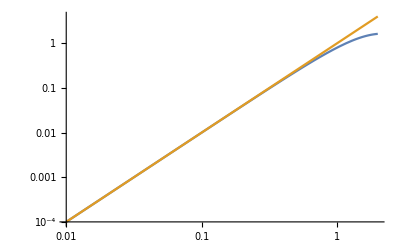

√(2-2 Cos[δt]^2 Cos[√2 δt]-(Csc[δt/2]^2 Sin[δt]^3 Sin[√2 δt])/(√2))

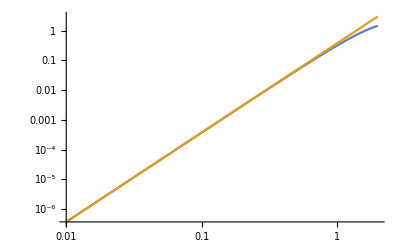

```mathematica
(* X, Y *)
Clear[δt,X,Y,U1,U2,U3, diff2,diff3]
{X,Y}={PauliMatrix[1],PauliMatrix[2]};
X.Y-Y.X;

(* first order Suzuki-Trotter decomposition *)
U1=MatrixExp[-I(X+Y)δt];
U2=MatrixExp[-I(X)δt].MatrixExp[-I(Y)δt];
diff2=Refine[Norm[U1-U2],{δt>0}]//Simplify
LogLogPlot[{diff2,δt^2},{δt,0.01,2}]

(* second order Suzuki-Trotter decomposition *)
U3=MatrixExp[-I(X)δt/2].MatrixExp[-I(Y)δt].MatrixExp[-I(X)δt/2]//Simplify;
diff3=Refine[Norm[U1-U3],{δt>0}]//Simplify
(*Series[diff3,{δt,0,3}]*)
LogLogPlot[{diff3,(√5/6) δt^3},{δt,0.01,2}]
```

```mathematica
(* X, Z *)
Clear[δt,X,Z,Y,U1,U2,U3, diff2,diff3]
{X,Z}={PauliMatrix[1],PauliMatrix[3]};
X.Z-Z.X;

(* first order Suzuki-Trotter decomposition *)
U1=MatrixExp[-I(X+Z)δt];
U2=MatrixExp[-I(X)δt].MatrixExp[-I(Z)δt];
diff2=Refine[Norm[U1-U2],{δt>0}]//FullSimplify
LogLogPlot[{diff2,δt^2},{δt,0.01,2}]


(* second order Suzuki-Trotter decomposition *)
U3=MatrixExp[-I(X)δt/2].MatrixExp[-I(Z)δt].MatrixExp[-I(X)δt/2]//Simplify;
diff3=Refine[Norm[U1-U3],{δt>0}]//FullSimplify
(*Series[diff3,{δt,0,3}]*)
LogLogPlot[{diff3,(√5/6) δt^3},{δt,0.01,2}]
```

√(2-2 Cos[δt]^2 Cos[√2 δt]-√2 Sin[2 δt] Sin[√2 δt])

-Graphics-

√(2-2 Cos[δt]^2 Cos[√2 δt]-(Csc[δt/2]^2 Sin[δt]^3 Sin[√2 δt])/(√2))

-Graphics-